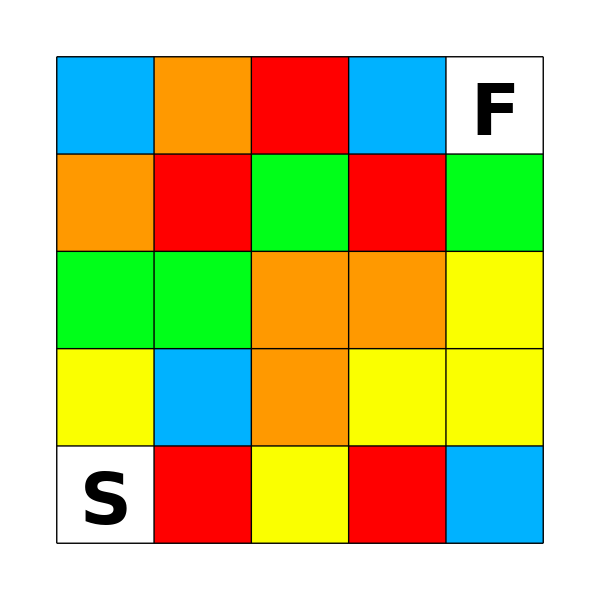

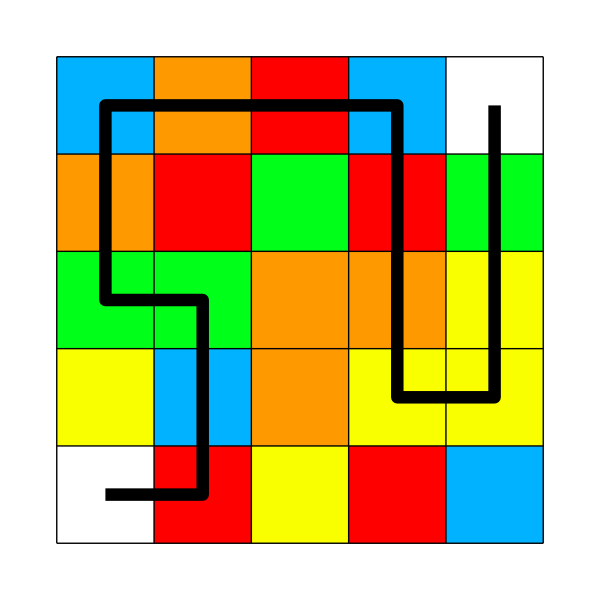

```mathematica
d[{x1_,y1_},{x2_,y2_}]:=(x2-x1)^2+(y2-y1)^2
```

```mathematica
col={GrayLevel[1],Hue[0],Hue[.17],Hue[.55],Hue[.35],Hue[.1],Hue[.75],GrayLevel[.5]};
```

```mathematica
shapes={nothing,star,square,triangle,plus,circle};
```

```mathematica
nothing[i_,j_]:={}
```

```mathematica
square[i_,j_]:=Style[Rectangle[{i-1/6,j-1/6},{i+1/6,j+1/6}],Antialiasing->False]
```

```mathematica
circle[i_,j_]:={LightGray,Disk[{i,j},1/4],Black,AbsoluteThickness[2],Circle[{i,j},1/4]}
```

```mathematica
triangle[i_,j_]:={AbsoluteThickness[2],Line[{{i-.3,j-.25},{i+.3,j-.25},{i,j+.25},{i-.3,j-.25}}]}
```

```mathematica
pp[angle_]:=.4{Cos[2Pi angle/5+Pi/10],Sin[2Pi angle/5+Pi/10]}
```

```mathematica
star[i_,j_]:=Polygon[{{i,j}+pp[1],{i,j}+pp[3],{i,j}+pp[5],{i,j}+pp[2],{i,j}+pp[4]}]
```

```mathematica
plus[i_,j_]:={AbsoluteThickness[3],Line[{{i,j-.25},{i,j+.25}}],Line[{{i-.25,j},{i+.25,j}}]}
```

```mathematica
draw[L_]:=Module[{},Print[Graphics[{Table[{col⟦c[{i,j}]⟧,Rectangle[{i-1/2,j-1/2},{i+1/2,j+1/2}]},{i,1,n},{j,1,m}],Style[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}]},Antialiasing->False],Text[Style["S",FontSize->20,FontWeight->"Bold"],{1,1-0.1}],Text[Style["F",FontSize->20,FontWeight->"Bold"],{n,m-0.1}]},AspectRatio->Automatic,PlotRange->{{1/2-.02,n+1/2+.02},{1/2-.02,m+1/2+.02}},ImageSize->20 {n,m}]];Print[Graphics[{Table[{col⟦c[{i,j}]⟧,Rectangle[{i-1/2,j-1/2},{i+1/2,j+1/2}]},{i,1,n},{j,1,m}],
Style[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}]},Antialiasing->False],AbsoluteThickness[3],Line[L]},AspectRatio->Automatic,PlotRange->{{1/2-.02,n+1/2+.02},{1/2-.02,m+1/2+.02}},ImageSize->20 {n,m}]]]
```

```mathematica
drawshapes[L_]:=Module[{},Print[Graphics[{Table[shapes⟦c[{i,j}]⟧[i,j],{i,1,n},{j,1,m}],Style[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}]},Antialiasing->False],Text[Style["S",FontSize->20,FontWeight->"Bold"],{1,1-0.1}],Text[Style["F",FontSize->20,FontWeight->"Bold"],{n,m-0.1}]},AspectRatio->Automatic,PlotRange->{{1/2-.02,n+1/2+.02},{1/2-.02,m+1/2+.02}},ImageSize->20 {n,m}+1]];Print[Graphics[{Table[shapes⟦c[{i,j}]⟧[i,j],{i,1,n},{j,1,m}],
Style[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}]},Antialiasing->False],AbsoluteThickness[3],Red,Line[L],Black,Text[Style["S",FontSize->20,FontWeight->"Bold"],{1,1-0.1}],Text[Style["F",FontSize->20,FontWeight->"Bold"],{n,m-0.1}]},AspectRatio->Automatic,PlotRange->{{1/2-.02,n+1/2+.02},{1/2-.02,m+1/2+.02}},ImageSize->20 {n,m}+1]]]
```

```mathematica
paths:=Module[{},
p={{{1,1}}};
done={};
While[Length[p]>0,
path=Last[p];
p=Reverse[Rest[Reverse[p]]];
pos=Last[path];
If[pos=={n,m},
AppendTo[done,path],touch=Select[A,d[#,pos]==1&&Not[MemberQ[path,#]]&]; p=p~Join~Map[path~Join~{#}&,touch]]];
done]
```

```mathematica
equ[L_]:=Module[{},
cts=Map[c,L];
u=Union[Table[Count[cts,i],{i,2,colors+1}]];
Length[u]==1&&u[[1]]>1]
```

```mathematica
n=5;
m=5;
colors=5;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
```

```mathematica
door=paths;
```

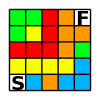

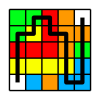

$Aborted

```mathematica
For[trial=1,trial≤1000000,trial++,For[i=1,i≤n,i++,For[j=1,j≤m,j++,c[{i,j}]= RandomInteger[{2, colors+1}]]];c[{1,1}]=1;
c[{n,m}]=1;
y=c/@A;
If[And@@Table[Count[y,i]>3,{i,2,colors+1}],
sols={};
For[i=1,i≤Length[door],i++,If[equ[door⟦i⟧],AppendTo[sols,door⟦i⟧];If[Length[sols]>1,Break[]]]];If[Length[sols]==1,draw/@sols]]]
```

```mathematica
For[trial=1,trial≤10000000,trial++,For[i=1,i≤n,i++,For[j=1,j≤m,j++,c[{i,j}]=Floor[1/2 RandomInteger[{2,2 colors+3}]]]];c[{1,1}]=1;
c[{n,m}]=1;
y=c/@A;
If[And@@Table[Count[y,i]≥Ceiling[(n m-2)/(colors+2)],{i,2,colors+1}],
sols={};
For[i=1,i≤Length[door],i++,If[equ[door⟦i⟧],AppendTo[sols,door⟦i⟧];If[Length[sols]>1,Break[]]]];If[Length[sols]==1,drawshapes/@sols]]]
```

$Aborted

## 6x6 - 5 colors

## 5x5 - 6 colors

## 5x5 - 5 colors

## 5x5 - 4 colors

## 5x5 - 3 colors

## 4x4 - 3 colors